Units: [GeV]
L= c_bs 1/(2 Λ) s γ^μ b δa + c_ee 1/(2 Λ) e γ^μ e δa

```mathematica
NotebookSave[];
```

```mathematica
SetDirectory[ NotebookDirectory[]];
```

### Display

Short-Hands to give all plots a consistent look and collect labels that will be used several times

```mathematica
colours={ColorData[10,6],ColorData[10,1],ColorData[10,5],ColorData[10,3],ColorData[10,8],ColorData[10,2],ColorData[10,7],ColorData[10,4],ColorData[10,9]}
```

{RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275]}

```mathematica
styles={Directive[colours[[1]],Dashed],Directive[colours[[2]],Dashed],Directive[colours[[1]],Dotted],colours[[2]],colours[[1]],colours[[3]],colours[[4]],colours[[5]]};
```

```mathematica
legends={"K_S, m_a=0.3GeV","K_S, m_a=0.05GeV", "D, m_a=0.3GeV", "B^+, m_a=0.05GeV", "B^+, m_a=0.3GeV", "B^+, m_a=1GeV", "B^+, m_a=2GeV", "B^+, m_a=4GeV"};
```

```mathematica
disp={PlotLegends->legends,PlotStyle->styles,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
dispH={ChartLegends->legends,ChartStyle->styles,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
```

```mathematica
basicdisp={AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
```

```mathematica
xgrid={Log[10^(-6)],Log[2*10^(-6)],Log[3*10^(-6)],Log[4*10^(-6)],Log[5*10^(-6)],Log[6*10^(-6)],Log[7*10^(-6)],Log[8*10^(-6)],Log[9*10^(-6)],Log[10^(-5)],Log[2*10^(-5)],Log[3*10^(-5)],Log[4*10^(-5)],Log[5*10^(-5)],Log[6*10^(-5)],Log[7*10^(-5)],Log[8*10^(-5)],Log[9*10^(-5)],Log[10^(-4)],Log[2*10^(-4)],Log[3*10^(-4)],Log[4*10^(-4)],Log[5*10^(-4)],Log[6*10^(-4)],Log[7*10^(-4)],Log[8*10^(-4)],Log[9*10^(-4)],Log[10^(-3)],Log[2*10^(-3)],Log[3*10^(-3)],Log[4*10^(-3)],Log[5*10^(-3)],Log[6*10^(-3)],Log[7*10^(-3)],Log[8*10^(-3)],Log[9*10^(-3)],Log[1*10^(-2)],Log[2*10^(-2)],Log[3*10^(-2)],Log[4*10^(-2)],Log[5*10^(-2)],Log[7*10^(-2)],Log[8*10^(-2)],Log[9*10^(-2)],Log[1*10^(-1)],Log[2*10^(-1)],Log[3*10^(-1)],Log[4*10^(-1)],Log[5*10^(-1)],Log[6*10^(-1)],Log[7*10^(-1)],Log[8*10^(-1)],Log[9*10^(-1)],Log[1],Log[2],Log[3],Log[4],Log[5],Log[6],Log[7],Log[8],Log[9],Log[10]};
```

```mathematica
cees=Table[10^(i),{i,Join[Range[-10,-5,1],Range[-5,1,0.05],Range[1,5,1]]}];
```

### Form-factors

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24,ΓtotalB:>6.582*10^-25/(10^-12 1.638)(*GeV*),ΓtotalK :>6.582*10^-25/(10^-8 1.2380)(*GeV*)};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188,vev:>246.22, mKstarV892:>0.892, mKstarV1410:>1.41, mKstarV1680:>1.72,mKAV1270:>1.27,mKAV1400:>1.4,mKstarS700:>0.7,mKstarS1430:>1.43};

ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

```mathematica
ClearAll[f0Kπ,f0Kπlist]
```

```mathematica
f0Kπ=Interpolation[{{0.0,0.9711},{0.0184,0.9840},{0.0369,0.9976},{0.0553,1.0117},{0.0737,1.0264},{0.0922,1.0419},{0.1106,1.0581},{0.1290,1.0753}}];(*1602.04113*)
```

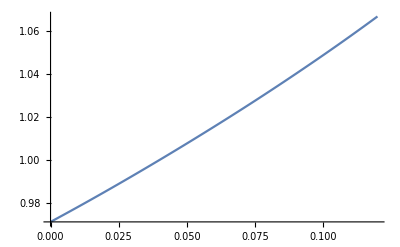

```mathematica
Plot[f0Kπ[x],{x,0,0.12}]
```

### ALP production branching fractions

```mathematica
BRBtoKPa[ma_,gabs_]:=1/ΓtotalB mB^3/(64 π) Abs[gabs]^2(1-mK^2/mB^2)^2 fzero[ma^2]^2 √((1-(ma+mK)^2/mB^2)(1-(ma-mK)^2/mB^2)) /.constants/.formFactors/.values/.masses/.ckms
BRKtoπPa[ma_,gabs_]:=1/ΓtotalK mK^3/(64 π) Abs[gabs]^2(1-mπ^2/mK^2)^2 f0Kπ[ma^2]^2 √((1-(ma+mπ)^2/mK^2)(1-(ma-mπ)^2/mK^2)) /.constants/.formFactors/.values/.masses/.ckms (*1901.02031*)
```

#### max(g_bs) allowed by semi-invisible meson decays

```mathematica
masslist=PowerRange[0.25,4.7,1.1] (*GeV, from 1612.07818*);
τlist=PowerRange[10^-1,10^3,1.5](* ps, from 1612.07818*);
```

The upper bound on the ALP-quark couplings come from the measurements of BR(K -> π+ inv ) for ma<mK-mπ and BR(B -> K + inv ) for  mK-mπ < ma< mB-mK. 
BR(K -> π+ inv ): At E787 & E949 the limits are 1.73 10^-10 (for 150 MeV<ma<260 MeV) and 2.2 10^-9 (for ma< 115 MeV) . The SM predicts  9.11 10^-11. At NA62 II we expect the bound to go down to 1.4 10^-9 [1811.08508]
BR(B -> K + inv ): At Belle, the upper limit is 1.6 10^-5 [1901.02031] and the SM predicts  4 10^-6 [1409.4557]. At Belle II we expect the bound to go down to O(10%) relative to the SM value [1901.02031].

```mathematica
BRBtoKPaBelle=1.6 10^-5-4 10^-6;
BRBtoKPaBelleII=4 10^-6(1+0.1);

BRKtoπaE787=1.73 10^-10-9.11 10^-11;
BRKtoπaE949=2.2 10^-9-9.11 10^-11;
BRKtoπaNa62=1.4 10^-9-9.11 10^-11;
```

At the moment, the K-> π^0 a(m=m_(π^0)) region is not cut out

```mathematica
gabsCurrent[x_]:=Piecewise[{{NSolve[BRBtoKPa[x,gg]==BRBtoKPaBelle,gg][[2,1,2]],x<(mB-mK)&&x>(mK-mπ)/.masses},{NSolve[BRKtoπPa[x,gg]==BRKtoπaE949,gg][[2,1,2]],x<(mK-mπ)/.masses}}]
(*gabsFuture[x_]:=Piecewise[{{NSolve[BRBtoKPa[x,gg]==BRBtoKPaBelleII,gg][[2,1,2]],x<(mB-mK)&&x>(mK-mπ)/.masses},{NSolve[BRKtoπPa[x,gg]==BRKtoπaNa62,gg][[2,1,2]],x<(mK-mπ)/.masses}}]*)
```

```mathematica
gabsMAXlistCurrent=gabsCurrent/@masslist;
(*gabsMAXlistFuture=gabsFuture/@masslist;*)
```

#### BR(B-> K μμ) for max(g_bs)

For now, assume 100% decay to muons -> lifetime is determined by c_μμ

```mathematica
BRBtoKμμList=PowerRange[10^-10,10^-7,2]//N;
```

```mathematica
NSolve[BRBtoKPa[masslist[[1]],gabs]==BRBtoKμμList[[1]],gabs][[2,1,2]]
```

2.28097×10^-11

```mathematica
NSolve[BRBtoKPa[masslist[[1]],gabs]==BRBtoKμμList[[-1]],gabs][[2,1,2]]
```

5.16125×10^-10

```mathematica
paramListTitle="# m [GeV], tau [ps], csb, BR_theo(B->K mu mu)\n";
paramList={};
```

```mathematica
For[i=1,i<Length[masslist]+1,i++,For[j=1,j<Length[τlist]+1,j++,For[k=1,k<Length[BRBtoKμμList]+1,k++,paramList=Append[paramList,{masslist[[i]], τlist[[j]], NSolve[BRBtoKPa[masslist[[i]],gabs]==BRBtoKμμList[[k]],gabs][[2,1,2]],BRBtoKμμList[[k]]}]]]]
```

```mathematica
file=OpenWrite["m-tau-cabs-BRBtoKmumu.tsv",PageWidth->Infinity];
WriteString[file,paramListTitle];
Export[file,paramList];
Close[file];
```